# Statistische Mechanik Bonusblatt

```mathematica
ClearAll["Global`*"]
```

## Helpful Functions

This formats quantities with errors

```mathematica
f[{a_,b_}]:=NumberForm[SetAccuracy[a±b,Accuracy@SetPrecision[b,2]],ExponentFunction->(Null&)]//Quiet
```

## Regression

```mathematica
gaussReg[xdata_,ydata_,dydata_]:=With[{Δ=Total[1/#^2&/@ dydata]Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[xdata]}]-(Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[xdata]}])^2},{1/Δ(Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}] Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), 1/Δ(Total[1/#^2&/@ dydata]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), Sqrt[1/Δ Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]], Sqrt[1/Δ Total[1/#^2&/@ dydata]]} ]
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

## Random Walk

### Data

```mathematica
NExperiments = 1000000;
```

```mathematica
L=200;
```

```mathematica
randomWalkData=Import[NotebookDirectory[]<>"randomWalk.csv"][[All,1;;-2]];
```

```mathematica
R2=randomWalkData[[1]]
```

{0,1,1.99953,2.99732,3.9984,5.00284,6.00345,7.00193,8.0022,8.99908,10.0009,11.0008,11.9949,12.9958,13.995,15.0014,15.9996,17.0024,18.0006,18.9977,20.0078,21.0081,22.0145,23.0148,24.0182,25.0151,26.0095,27.0063,28.0202,29.0145,30.0139,31.0122,32.0155,33.0121,34.017,35.0246,36.0137,37.0061,38.0134,39.016,40.0246,41.0575,42.0512,43.0342,44.0379,45.0409,46.0489,47.0431,48.0501,49.0634,50.0503,51.047,52.0513,53.0524,54.0541,55.0586,56.0526,57.041,58.0489,59.0519,60.0537,61.0716,62.0487,63.0442,64.0473,65.0611,66.0654,67.0621,68.0747,69.0898,70.0922,71.0893,72.0894,73.0961,74.0839,75.0906,76.0741,77.0637,78.0913,79.1052,80.1187,81.12,82.1236,83.1003,84.1105,85.1005,86.1004,87.0857,88.0833,89.1129,90.1212,91.1238,92.1354,93.1434,94.1489,95.145,96.1351,97.1415,98.1369,99.1324,100.149,101.147,102.148,103.154,104.171,105.16,106.163,107.168,108.161,109.179,110.171,111.144,112.126,113.134,114.15,115.147,116.167,117.181,118.184,119.186,120.177,121.213,122.228,123.241,124.212,125.238,126.229,127.252,128.24,129.217,130.216,131.209,132.189,133.159,134.154,135.168,136.168,137.166,138.169,139.144,140.167,141.14,142.131,143.158,144.176,145.189,146.187,147.193,148.171,149.148,150.119,151.141,152.113,153.088,154.105,155.121,156.114,157.099,158.066,159.086,160.088,161.094,162.068,163.079,164.059,165.021,166.006,166.978,167.986,169.004,169.996,171.005,171.97,172.952,173.954,174.982,175.976,176.978,177.971,178.994,179.981,181.003,182.013,183.018,184.004,184.994,185.985,186.984,188.006,189.012,190.029,191.022,192.03,192.995,193.995,194.996,195.988,197.002,198.047,199.039,200.004}

```mathematica
dR2= #[[2]]/Sqrt[NExperiments]&/@Transpose[randomWalkData];
```

```mathematica
randomWalkDataProcessed = Transpose[{Range[0,L],Around@@#&/@Transpose[{R2,dR2}]}];
```

```mathematica
regPars=ungewichteterReg[Range[0,L],R2]
```

{0.0522192,1.00024,0.0101261,0.000087585}

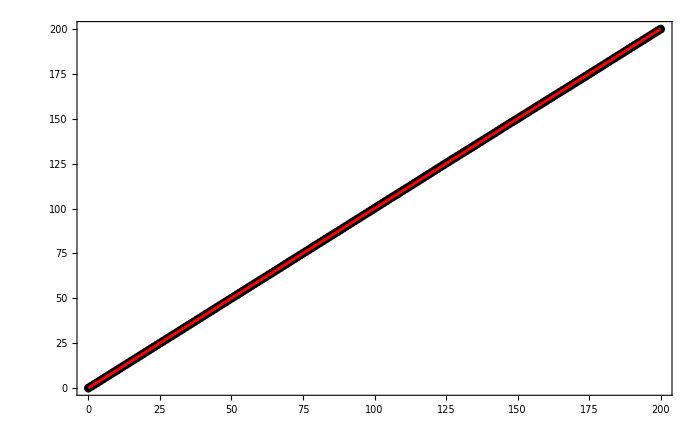

```mathematica
Show[ListPlot[randomWalkDataProcessed,Frame->True,ImageSize->700,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->Black,FrameTicksStyle->Directive[15,Opacity[1],FontOpacity[1]]],Plot[regPars[[1]] +regPars[[2]] x,{x,0,200},PlotStyle->Directive[Red,Thickness[0.003]]]]
```

```mathematica
Export[NotebookDirectory[]<>"abgabe/fig2a.pdf", Show[ListPlot[randomWalkDataProcessed,Frame->True,ImageSize->700,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->Black,FrameTicksStyle->Directive[15,Opacity[1],FontOpacity[1]]],Plot[regPars[[1]] +regPars[[2]] x,{x,0,200},PlotStyle->Directive[Red,Thickness[0.003]]]],Background->None];
```

```mathematica
Transpose[{Range[0,L], f[{#[[1]],#[[2]]/Sqrt[NExperiments]}]&/@Transpose[randomWalkData]}]//TeXForm//CopyToClipboard
```

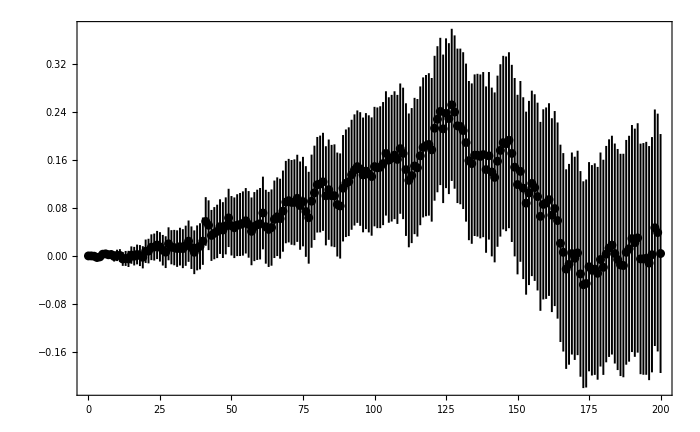

```mathematica
ListPlot[{#[[1]],#[[2]]-#[[1]]}&/@randomWalkDataProcessed,Frame->True,ImageSize->700,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[15,Opacity[1],FontOpacity[1]],Axes->None]
```

```mathematica
Export[NotebookDirectory[]<>"abgabe/fig2b.pdf", ListPlot[{#[[1]],#[[2]]-#[[1]]}&/@randomWalkDataProcessed,Frame->True,ImageSize->700,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[15,Opacity[1],FontOpacity[1]],Axes->None],Background->None];
```

### Trajectories

```mathematica
trajectoriesData=Import[NotebookDirectory[]<>"trajectories.csv"];
```

```mathematica
trajectories=Partition[trajectoriesData,L];
trajectories=Join[{{0,0}}, #]&/@trajectories;
```

```mathematica
cols=ColorData["M10DefaultDensityGradient"]/@Rescale[Range[20]]
```

{RGBColor[0.148, 0.33, 0.54],RGBColor[0.2143157894736842, 0.3668421052631579, 0.6021052631578948],RGBColor[0.2822368421052632, 0.4028947368421053, 0.6531578947368422],RGBColor[0.36460526315789477, 0.4318421052631579, 0.6047368421052632],RGBColor[0.4469736842105263, 0.4607894736842105, 0.5563157894736842],RGBColor[0.529342105263158, 0.48973684210526314, 0.5078947368421053],RGBColor[0.6117105263157894, 0.5186842105263157, 0.45947368421052637],RGBColor[0.694078947368421, 0.5476315789473684, 0.41105263157894745],RGBColor[0.7764473684210527, 0.5765789473684211, 0.3626315789473684],RGBColor[0.8588157894736841, 0.6055263157894737, 0.31421052631578955],RGBColor[0.906578947368421, 0.6364473684210527, 0.3103947368421052],RGBColor[0.9197368421052632, 0.6693421052631578, 0.35118421052631577],RGBColor[0.9328947368421052, 0.7022368421052632, 0.39197368421052625],RGBColor[0.9460526315789474, 0.7351315789473685, 0.43276315789473685],RGBColor[0.9592105263157895, 0.7680263157894737, 0.47355263157894734],RGBColor[0.9723684210526315, 0.800921052631579, 0.5143421052631578],RGBColor[0.9855263157894737, 0.8338157894736842, 0.5551315789473683],RGBColor[0.9986842105263158, 0.8667105263157895, 0.5959210526315789],RGBColor[1., 0.9078947368421052, 0.6710526315789472],RGBColor[1, 0.95, 0.75]}

```mathematica
lines=Flatten[Transpose[{cols,Line/@trajectories}]];
```

```mathematica
plotMax = Max[Abs[Flatten[trajectories]]]
```

30

```mathematica
grid=Flatten[Table[{Line[{{i,-plotMax},{i,plotMax}}], Line[{{-plotMax,i},{plotMax,i}}]},{i,-plotMax,plotMax}]];
```

```mathematica
Length/@trajectories
```

{200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200}

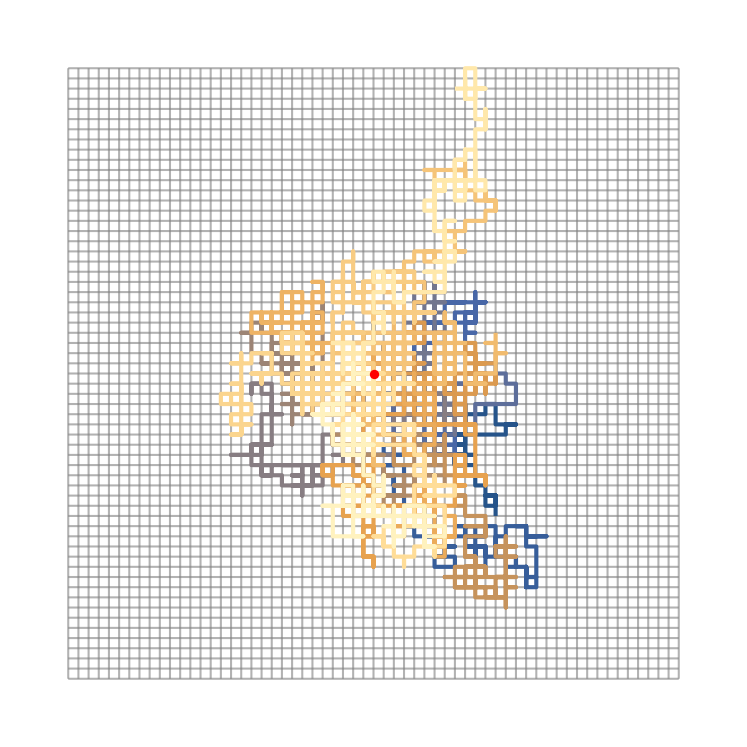

```mathematica
Graphics[{Thickness[0.002],Opacity[0.6], Gray, grid,Thickness[0.004],Opacity[1], lines, Red,PointSize[0.009],Point[{0,0}]}]
```

```mathematica
Export[NotebookDirectory[]<>"abgabe/fig1a.pdf",Graphics[{Thickness[0.002],Opacity[0.6], Gray, grid,Thickness[0.004],Opacity[1], lines, Red,PointSize[0.009],Point[{0,0}]}],Background->None];
```

## Random Avoiding Walk

### Data

```mathematica
NAvoidingExperiments = 10000;
LAvoiding = 30;
```

```mathematica
randomAvoidingWalkData=Import[NotebookDirectory[]<>"randomAvoidingWalk.csv"][[All,1;;-2]]
```

{{0,1,2.7046,4.798,7.3878,10.2316,13.3762,16.752,20.3266,24.1232,28.2966,32.6132,36.9604,41.6224,46.4538,51.4916,56.7506,62.1828,67.722,73.244,78.8728,84.672,90.219,95.884,101.546,107.176,112.701,118.054,122.96,127.142,130.249},{0,0,0.955421,2.16879,3.48902,5.10915,6.85116,8.78202,10.9103,13.1156,15.5752,18.1275,20.6353,23.3292,26.2655,29.262,32.5487,35.7578,39.0802,42.4263,45.7396,49.2271,52.85,56.4836,60.1475,63.9425,68.1845,72.2153,76.4102,80.3126,83.8306}}

```mathematica
randomAvoidingWalkDataProcessed = Transpose[{Range[0,LAvoiding], Around[#[[1]],#[[2]]/Sqrt[NAvoidingExperiments]]&/@Transpose[randomAvoidingWalkData]}];
```

```mathematica
Transpose[{Range[0,LAvoiding], f[{#[[1]],#[[2]]/Sqrt[NAvoidingExperiments]}]&/@Transpose[randomAvoidingWalkData]}]//TeXForm//CopyToClipboard
```

```mathematica
pars2=ungewichteterReg[Log[Range[1,LAvoiding-3]], Log[randomAvoidingWalkData[[1,2;;-4]]]]
```

{-0.0181818,1.4603,0.00596773,0.00235923}

```mathematica
f[{Exp[pars2[[1]]],Exp[pars2[[1]]]pars2[[3]]}]//TeXForm//CopyToClipboard
f[{pars2[[2]], pars2[[4]]}]//TeXForm//CopyToClipboard
```

```mathematica
Length[Range[1,LAvoiding-2]]
Length[randomAvoidingWalkData[[1,2;;-3]]]
```

28

28

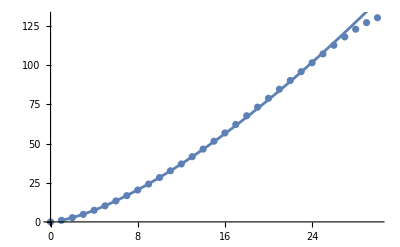

```mathematica
Show[ListPlot[randomAvoidingWalkDataProcessed], Plot[Exp[pars2[[1]]] x^pars2[[2]],{x,1,30}]]
```

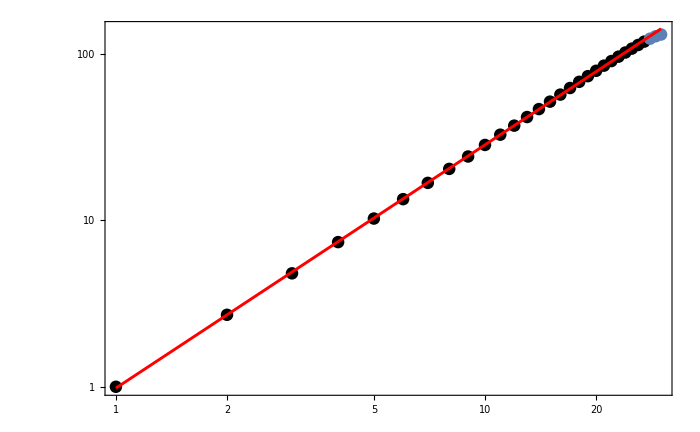

```mathematica
Show[ListLogLogPlot[randomAvoidingWalkDataProcessed[[1;;-4]],Frame->True,ImageSize->700,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->Black,FrameTicksStyle->Directive[15,Opacity[1],FontOpacity[1]]],ListLogLogPlot[randomAvoidingWalkDataProcessed[[-3;;]],PlotStyle->ColorData[97,1]], LogLogPlot[Exp[pars2[[1]]] x^pars2[[2]],{x,1,30},PlotStyle->Directive[Red,Thickness[0.003]]],PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"abgabe/fig2c.pdf",Show[ListLogLogPlot[randomAvoidingWalkDataProcessed[[1;;-4]],Frame->True,ImageSize->700,FrameStyle->Directive[Black,Thickness[0.003]],PlotStyle->Black,FrameTicksStyle->Directive[15,Opacity[1],FontOpacity[1]]],ListLogLogPlot[randomAvoidingWalkDataProcessed[[-3;;]],PlotStyle->ColorData[97,1]], LogLogPlot[Exp[pars2[[1]]] x^pars2[[2]],{x,1,30},PlotStyle->Directive[Red,Thickness[0.003]]],PlotRange->All],Background->None];
```

### Trajectories

```mathematica
trajectoriesAvoidingData=Import[NotebookDirectory[]<>"trajectoriesAvoiding.csv"];
```

```mathematica
trajectoriesAvoiding=Partition[trajectoriesAvoidingData,LAvoiding];
trajectoriesAvoiding=Join[{{0,0}}, #]&/@trajectoriesAvoiding;
```

```mathematica
linesAvoiding=Flatten[Transpose[{cols,Line/@trajectoriesAvoiding}]];
```

```mathematica
plotMaxAvoiding = Max[Abs[Flatten[trajectoriesAvoiding]]]
```

19

```mathematica
gridAvoiding=Flatten[Table[{Line[{{i,-plotMaxAvoiding},{i,plotMaxAvoiding}}],Line[{{-plotMaxAvoiding,i},{plotMaxAvoiding,i}}]},{i,-plotMaxAvoiding,plotMaxAvoiding}]];
```

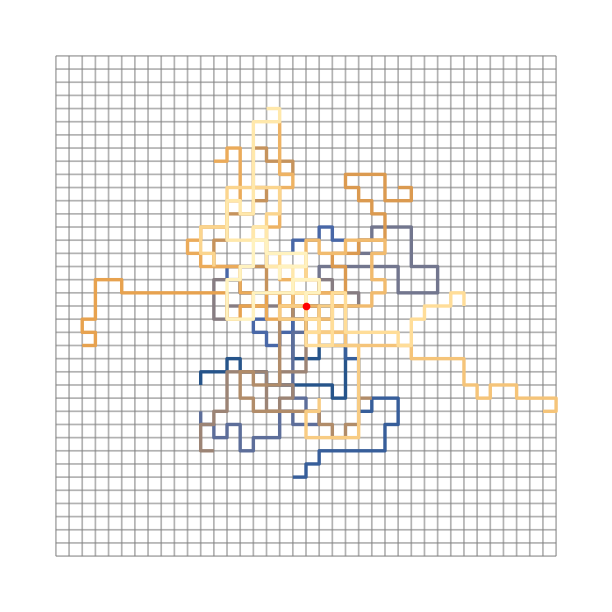

```mathematica
Graphics[{Thickness[0.002],Opacity[0.6], Gray, gridAvoiding,Thickness[0.004],Opacity[1], linesAvoiding, Red,PointSize[0.009],Point[{0,0}]}]
```

```mathematica
Export[NotebookDirectory[]<>"abgabe/fig1b.pdf",Graphics[{Thickness[0.002],Opacity[0.6], Gray, gridAvoiding,Thickness[0.004],Opacity[1], linesAvoiding, Red,PointSize[0.009],Point[{0,0}]}],Background->None];
```

## Other Plots

```mathematica
BarLegend[{"M10DefaultDensityGradient",{0,20}},19,LabelStyle->Directive[Black,12],Method->{FrameStyle->Thickness[0.1],TicksStyle->Directive[Black,Thickness[0.1]]}]
```

```mathematica
Export[NotebookDirectory[]<>"abgabe/fig1c.pdf",BarLegend[{"M10DefaultDensityGradient",{0,20}},19,LabelStyle->Directive[Black,12],Method->{FrameStyle->Thickness[0.02],TicksStyle->Directive[Black,Thickness[0.02]]}],Background->None];
```